## Slide 1

Introduction to the Quantum Theory of

OPEN SYSTEMS

Reed College Physics Seminar
13 February 2013

Dedecated to the memory of 
Richard E. Crandall (1947-2012)

Nicholas Wheeler

## Slide 2

## Overview:

### Composite Systems / Open Systems, and why they are of interest

### Essential Mathematical Notions

### Zurek's Decoherence Model

Evaporation of Information into Environment

### A Simple Dissipation Model

Evaporation of Energy into Environment

### Essentials of Quantum Measurement Theory

Idealized Perfect Meters

Imperfect Meters & their Uses

### Simultaneous Measurement of Conjugate Observables

Heisenberg Uncertainty Principle in a New Light

## Slide 3

# "Isolated" Mechanical Systems Do Not Exist

In classical/quantum mechanics we work theoretically with "isolated" systems, subject to the assumption that all "environmental" influences can be neglected…else subsumed in "impressed potentials" (no back action). But recall

• NEWTON'S BUCKET: Local inertia coordinated with "fixed stars."

• MACH'S PRINCIPLE: Mass/inertia meaningless in one particle universe  …conjectured to arise therefore by mysterious influence of remote masses…isotropy of mass/inertia implies effect is non-local, must be attributed to most remote masses. "When the subway jerks, it's the fixed stars that throw you down."

Einstein partly motivated by Mach's idea. Solution sought now in Higgs field? More speculatively, in "holographic" model of universe?

Experimentalists—who live in the real world—go to great pains to (approximately) isolate their systems.

Have always been amazed that experiments are possible… that one can place a bit of the universe on a bench top, tickle it without disturbing the universe, draw inferences that pertain to the whole. 

Can imagine toy universes (and spheres of human inquiry) in such "procedural reductionism" is not possible.

In short: "system isolation" is—like the "point mass" concept and (arguably) all physical concepts—an idealization, which we must on occasion be prepared to abandon. And by doing so we open up new vistas:

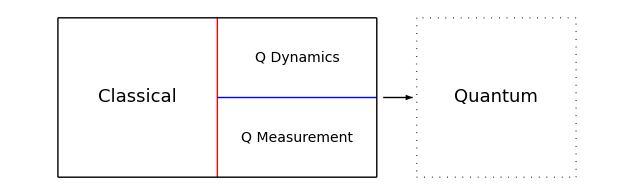

## Slide 3

# Composite Systems vs Open Systems

Composite systems are systems assembled—either formally ("mentally") or in physical fact—from subsystems 𝒮_1, 𝒮_2, ... , 𝒮_N.

ψ_1(x_1)ψ_2(x_2)⋯ψ_N(x_N)  :   Formally composite

ψ(x_1,x_2,⋯ ,x_N)              :   Physically composite, interactive

Open systems are composite systems assembed from system 𝒮 and an "environment" ℰ that typically has many degrees of freedom. If the pure states of 𝒮 and ℰ lived in finite-dimensional Hilbert spaces ℋ_𝒮, ℋ_ℰ and the conjunction were merely formal, would write

ψ_𝒮=(a_1
a_2)       ψ_ℰ=(b_1
b_2
b_3
b_4)

and to describe the state of the composite system 𝒮⊗ℰ borrow from matrix theory a device called the "Kronecker product":

ψ_𝒮⊗ψ_ℰ=(a_1 b_1
a_1 b_2
a_1 b_3
a_1 b_4
a_2 b_1
a_2 b_2
a_2 b_3
a_2 b_4)

But if the conjunction is physical (interactive) we must expect to write

ψ_(𝒮⊗ℰ)=(ψ_1
ψ_2
ψ_3
ψ_4
ψ_5
ψ_6
ψ_7
ψ_8)

Typially, such vectors cannot be Kronecker factored (displayed as Kronecker products). In such "non-separable" cases the states of 𝒮 and ℰ have become "entangled."

Linear operators on elements of ℋ_𝒮, ℋ_ℰ are described

𝔸=(a_11 | a_12
a_21 | a_22)       𝔹=(b_11 | b_12 | b_13 | b_14
b_21 | b_22 | b_23 | b_24
b_31 | b_32 | b_33 | b_34
b_41 | b_42 | b_43 | b_44)

which on ℋ_(𝒮⊗ℰ) give rise to

𝔸⊗ 𝔹 =(a_11 b_11 | a_11 b_12 | a_11 b_13 | a_11 b_14 | a_12 b_11 | a_12 b_12 | a_12 b_13 | a_12 b_14
a_11 b_21 | a_11 b_22 | a_11 b_23 | a_11 b_24 | a_12 b_21 | a_12 b_22 | a_12 b_23 | a_12 b_24
a_11 b_31 | a_11 b_32 | a_11 b_33 | a_11 b_34 | a_12 b_31 | a_12 b_32 | a_12 b_33 | a_12 b_34
a_11 b_41 | a_11 b_42 | a_11 b_43 | a_11 b_44 | a_12 b_41 | a_12 b_42 | a_12 b_43 | a_12 b_44
a_21 b_11 | a_21 b_12 | a_21 b_13 | a_21 b_14 | a_22 b_11 | a_22 b_12 | a_22 b_13 | a_22 b_14
a_21 b_21 | a_21 b_22 | a_21 b_23 | a_21 b_24 | a_22 b_21 | a_22 b_22 | a_22 b_23 | a_22 b_24
a_21 b_31 | a_21 b_32 | a_21 b_33 | a_21 b_34 | a_22 b_31 | a_22 b_32 | a_22 b_33 | a_22 b_34
a_21 b_41 | a_21 b_42 | a_21 b_43 | a_21 b_44 | a_22 b_41 | a_22 b_42 | a_22 b_43 | a_22 b_44)

(𝔸⊗𝔹)(ψ_𝒮⊗ψ_ℰ)=(𝔸ψ_𝒮)⊗(𝔹 ψ_ℰ)

but we must expect more generally to encounter matrices

ℂ =(c_11 | c_12 | c_13 | c_14 | c_15 | c_16 | c_17 | c_18
c_21 | c_22 | □ | □ | □ | □ | □ | □
□ | □ | c_33 | □ | □ | □ | □ | □
□ | □ | □ | c_44 | □ | □ | □ | □
□ | □ | □ | □ | c_55 | □ | □ | □
□ | □ | □ | □ | □ | c_66 | □ | □
□ | □ | □ | □ | □ | □ | c_88 | □
c_81 | □ | □ | □ | □ | □ | □ | c_88)

that cannot be displayed as Kronecker products.

The primary objective of the quantum theory of open systems is to describe the effect of ℰ upon the motion of 𝒮, and

The central problem is that the state of ℰ is known very imprecisely (and is anyway of no intrinsic interest). We are obliged therefore to proceed probabilistically. Two (interrelated) principal ways to proceed:

1. Devise stochastic equations of 𝒮-motion (think Brownian motion);

2. Say what one can about the motion of 𝒮⊗ℰ—thought of as a large closed system

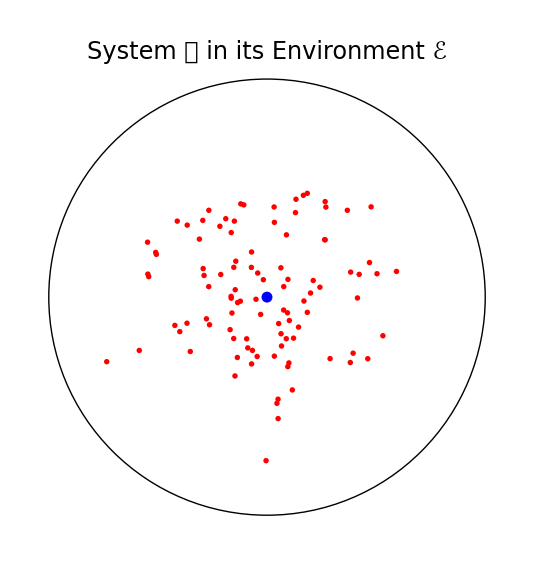

—and obtain 𝒮-dynamics by a projective technique.

## Slide 4

# Density Matrices & the Partial Trace

Standard quantum theory asserts that if 𝒮 is in state ψ then the expected mean of a series of A-measurements is

⟨A⟩ = (ψ |𝔸| ψ)

But it is an idealization to suppose that the states presented to the A-meter are ψ in every instance: they are "shot from imperfect ψ-guns," drawn from ensembles that are never pure. Suppose the ensemble produces

ψ_1 with probability p_1
ψ_2 with probability p_2

Then

⟨A⟩=p_1(ψ_1|𝔸|ψ_1)+p_2(ψ_2|𝔸|ψ_2)

Can be written

⟨A⟩ = Tr[𝔸 ρ]

where

ρ=|ψ_1)p_1(ψ_1|+|ψ_2)p_2(ψ_2|

is a "density matrix." Density matrices—introduced by Weyl and 
von Neumann—are in almost all contexts the preferred state descriptors (though they describe the states not of systems but of ensembles). Density matrices 

1. are manifestly hermitian,

2. are easily seen invariably to have unit trace,

3. are positive-semidefinite (all eigenvalues non-negative)

All matrices with those properties interpretable as density matrices.

REMARK: Classical mixtures can be described by recipes (how much of what). Quantum mixtures cannot: differently weighted mixtures of different states can result in the same density matrix.

When developed in its eigenbasis,

ρ=(r_1 | 0 | 0 | 0 | 0
0 | r_2 | 0 | 0 | 0
0 | 0 | r_3 | 0 | 0
0 | 0 | 0 | r_4 | 0
0 | 0 | 0 | 0 | r_5)   Impure mixture:  Tr[ρ] = 1, 0<Tr[ρ^2]<1

ρ=(0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)            Pure case:  Tr[ρ]=Tr[ρ^2]=1

Need "partial trace" (notion introduced by Dirac), defined

Tr_1[𝕄]=∑_(k=1)^2 (Transpose[u_k]⊗𝕀_4).𝕄.(u_k⊗𝕀_4)

Tr_2[𝕄]=∑_(k=1)^4 (𝕀_2⊗Transpose[v_k]).𝕄.(𝕀_2⊗v_k)

Tr_1[𝔸⊗𝔹]=((a_11+a_22) b_11 | (a_11+a_22) b_12 | (a_11+a_22) b_13 | (a_11+a_22) b_14
(a_11+a_22) b_21 | (a_11+a_22) b_22 | (a_11+a_22) b_23 | (a_11+a_22) b_24
(a_11+a_22) b_31 | (a_11+a_22) b_32 | (a_11+a_22) b_33 | (a_11+a_22) b_34
(a_11+a_22) b_41 | (a_11+a_22) b_42 | (a_11+a_22) b_43 | (a_11+a_22) b_44)

Tr_1[𝔸⊗𝔹]=Tr[𝔸]𝔹

Tr_2[𝔸⊗𝔹]=𝔸 Tr[𝔹]

Application does not require matrix to possess Kronecker factored structure:

ℂ=(c_11 | c_12 | c_13 | c_14 | c_15 | c_16 | c_17 | c_18
c_21 | c_22 | c_23 | c_24 | c_25 | c_26 | c_27 | c_28
c_31 | c_32 | c_33 | c_34 | c_35 | c_36 | c_37 | c_38
c_41 | c_42 | c_43 | c_44 | c_45 | c_46 | c_47 | c_48
c_51 | c_52 | c_53 | c_54 | c_55 | c_56 | c_57 | c_58
c_61 | c_62 | c_63 | c_64 | c_65 | c_66 | c_67 | c_68
c_71 | c_72 | c_73 | c_74 | c_75 | c_76 | c_77 | c_78
c_81 | c_82 | c_83 | c_84 | c_85 | c_86 | c_87 | c_88)

Tr_1[ℂ]=(c_11+c_55 | c_12+c_56 | c_13+c_57 | c_14+c_58
c_21+c_65 | c_22+c_66 | c_23+c_67 | c_24+c_68
c_31+c_75 | c_32+c_76 | c_33+c_77 | c_34+c_78
c_41+c_85 | c_42+c_86 | c_43+c_87 | c_44+c_88)

Tr_2[ℂ]=(c_11+c_22+c_33+c_44 | c_15+c_26+c_37+c_48
c_51+c_62+c_73+c_84 | c_55+c_66+c_77+c_88)

Enables us to "projectively" extract description of ρ_𝒮 from that of ρ_(𝒮⊗ℰ).

## Slide 5

# Zurek's Decoherence Model

The effects most characteristic of quantum mechanics (wave mechanics) are interference effects:

(ψ_1
ψ_2)^adj(a | z
z̄ | b)(ψ_1
ψ_2)=a ψ_1 (ψ̄)_1+z ψ_2 (ψ̄)_1+z̄ ψ_1 (ψ̄)_2+b ψ_2 (ψ̄)_2

=Tr[(a | z
z̄ | b).((ψ̄)_1 ψ_1 | (ψ̄)_2 ψ_1
(ψ̄)_1 ψ_2 | (ψ̄)_2 ψ_2)]

Those effects are seen to derive from off-diagonal elements of the density matrix. 

"Decoherence" is the name given to processes that kill those off-diagonal terms, and thus reduce quantum statistics to ordinary statistics.

Decoherence comes about spontaneously as a result of interaction with the environment (information initially resident in 𝒮 evaporates into ℰ, as was discussed here just one year ago by Max Schlosshauer), and quantum mechanics degenerates into a probabilistic version of classical mechanics.

A tractable model of such a process was devised in 1982 by Wohciech Zurek

—then at the threshold of his illustrious career—of which I present a bare-bones instance.

Zurek takes 𝒮 to be a qubit (2-state system), and ℰ to be a population of N qubits:

-Graphics3D-

I assign to N the absurdly small value of N = 2. 

One expects the composite Hamiltonian to be of the form

ℍ=ℍ_𝒮+ℍ_int+ℍ_ℰ

but we set ℍ_𝒮=ℍ_ℰ=𝕆 and—writing

𝕀=(1 | 0
0 | 1)       σ=(1 | 0
0 | -1)

assign to ℍ_int the structure

ℍ_int=σ⊗(g_1 σ⊗𝕀+g_2 𝕀⊗σ)

=(g_1+g_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | g_1-g_2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -g_1+g_2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -g_1-g_2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -g_1-g_2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -g_1+g_2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | g_1-g_2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | g_1+g_2)

where the gs are coupling constants. It is the diagonal structure of ℍ_int that makes the model tractable. 

The global unitary propagator is

𝕌[t]=Exp[-i ℍ_int t]

(ⅇ^(-ⅈ (t g_1+t g_2)) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ⅇ^(-ⅈ (t g_1-t g_2)) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ⅇ^(ⅈ (t g_1-t g_2)) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ⅇ^(ⅈ (t g_1+t g_2)) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ⅇ^(ⅈ (t g_1+t g_2)) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ⅇ^(ⅈ (t g_1-t g_2)) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(-ⅈ (t g_1-t g_2)) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(-ⅈ (t g_1+t g_2)))

Assuming the initial state of the global system to possess the factored structure

ψ_initial=(a_1 b_1
a_1 b_2
a_1 b_3
a_1 b_4
a_2 b_1
a_2 b_2
a_2 b_3
a_2 b_4)

with a_1^2+a_2^2==1,b_1^2+b_2^2+b_3^2+b_4^2==1 we construct first ρ_initial, then

ρ[t]=𝕌[t]ρ_initial 𝕌_adj[t]

and finally the partial trace that describes the moving state of 𝒮:

𝕊[t]=Tr_ℰ[ρ[t]]=(S_11(t) | S(t)
S^*(t) | S_22(t))

The diagonal elements are found to be constant

S_11(t)=a_1 a_1                 S_22(t)=a_2 a_2

and to preserve the unit trace condition, while the off-diagonal elements are a moving complex number (and its conjugate):

S(t)=a_1 a_2{f(t)+i g(t)}

where

f(t)=Cos[2 t (g_1+g_2)] b_1^2+Cos[2 t (g_1-g_2)] b_2^2+Cos[2 t (g_1-g_2)] b_3^2+Cos[2 t (g_1+g_2)] b_4^2
g(t)=-Sin[2 t (g_1+g_2)] b_1^2-Sin[2 t (g_1-g_2)] b_2^2+Sin[2 t (g_1-g_2)] b_3^2+Sin[2 t (g_1+g_2)] b_4^2

are dictated by the initial state of ℰ (and the coupling constants).

Assign random norm-preserving values to the b-coordinates and to the coupling constants, find S(t) traces figures like this on the complex plane:

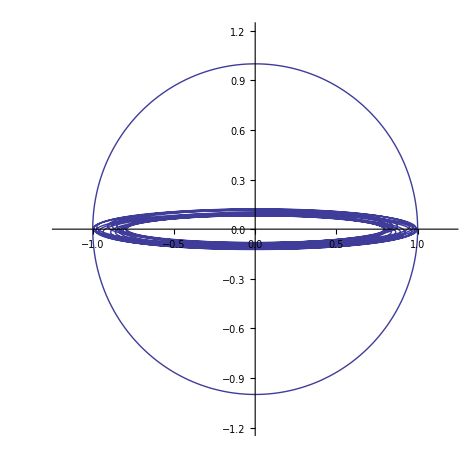

Evidently S(t) does not vanish. But look to its time-average over a brief inertial interval…

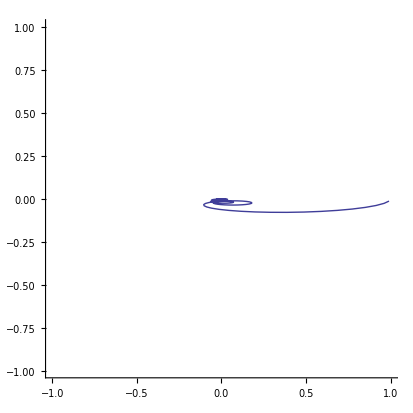

and over a brief interval at a later time (note the reduced scale):

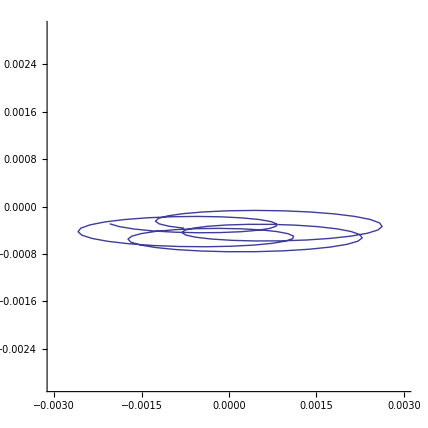

Introduce a 3rd environmental qubit and get

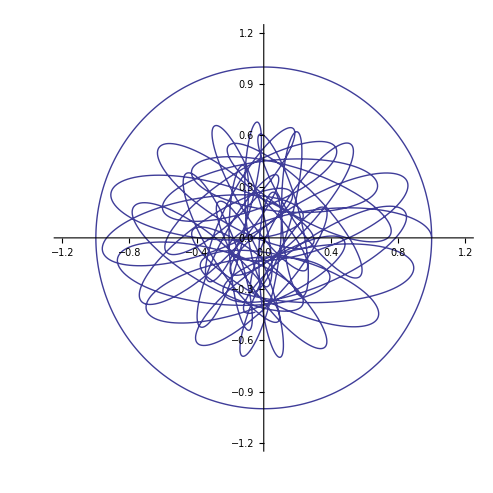

which when time-averaged over an initial interval gives

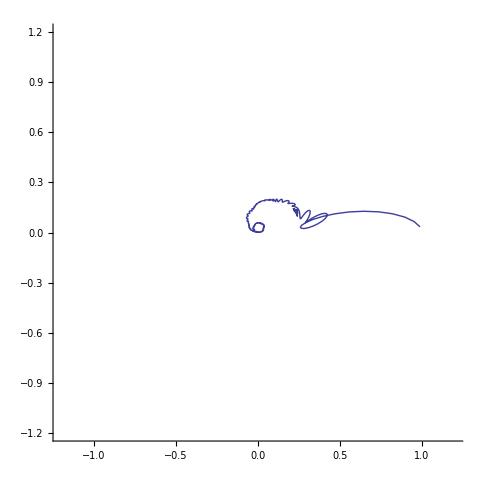

and when time-averaged over a brief later interval gives

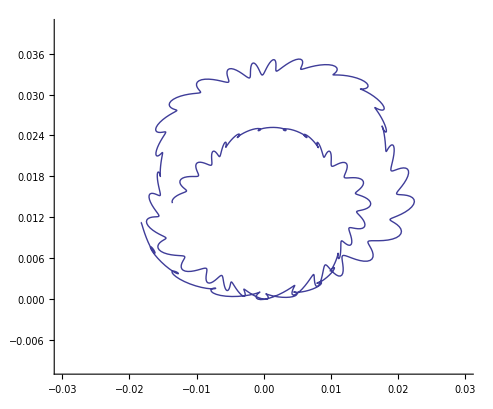

As more qubits are introduced into the environment the time-averaged extinction of the off-diagonal element becomes rapidly
  • more complex in its details
  • swifter
  • more perfect.
  
So we have

(p_1 | ■
■ | p_2)⟹(p_1 | 0
0 | p_2)    Environmentally induced

and if we introduce a term ℍ_𝒮 into the global Hamiltonian can set the diagonal terms into motion. Long way from here to a convincing account of the emergence of the classical world… but its a start.

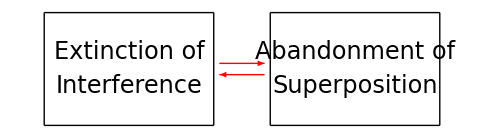

EVAPORATION OF INFORMATION:

Environmentally-induced extinction of off-diagonal elements (decoherence) is accompanied by a transfer of information from 𝒮 to ℰ. 

The von Neumann entropy of an ensemble of states is defined

Entropy=-Tr[ρ log ρ]=-∑_k λ_k log λ_k

The most general 2 × 2 density matrix has the form

ρ=(a | zⅇ^(+iϕ)
ze^-iϕ | 1-a)

where z ranges on 0 ⩽ z ⩽ z_max and z_max=√(a(1-a)) arises from the requirement that all eigenvalues of ρ by non-negative: equivalently, that

Tr[ρ^2] ⩽ 1

The eigenvalues of ρ are

λ_1=1/2-√(1/4 (-1+2 a)^2+z^2)
λ_2=1/2+√(1/4 (-1+2 a)^2+z^2)

which we use to construct the function Entropy[a,z]

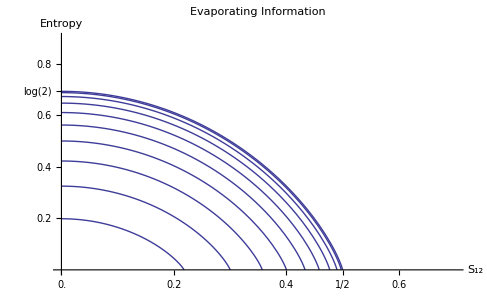

The curves rise as a advances 0 ⟶ 1/2,  descent as it continues its advance 1/2 ⟶ 1.

Entropy is a unitary invariant, so the global entropy is t-independent. 

But as z descends 0 ⟵ z the entropy is seen to increase: decoherence caused information initially resident in 𝒮 to evaporate into ℰ.

This means that the dynamical motion of ρ_𝒮 must be non-unitary.

Further evidence of non-unitarity emerges when one looks to the evolution of Tr[ρ_𝒮^2]. Traces of all powers are unitary invariants, but we find

Evolution of Tr[ρ_𝒮^2]

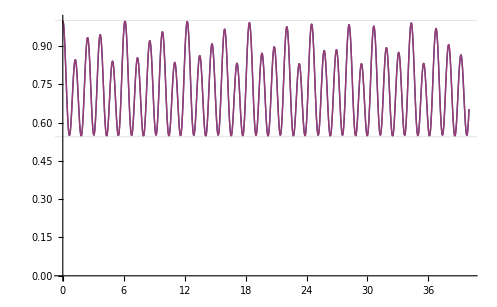

Quantum computers are unitarily controlled quantum interference devices. Now very easy to see how environmental noise—very difficult to prevent—can render them inoperative.

## Slide 6

# Lindblad's Equation & a Dissipation Model

In the 1970s people (Kossakowski, Sudarshan, Lindblad, others) addressed this question: How to describe—intrinsically, without explicit reference to ℰ—the non-unitary motion of

ρ_𝒮=Tr_ℰ[ρ_(𝒮⊗ℰ)]

that is induced by the unitary motion of ρ_(𝒮⊗ℰ) ?

The "Lindblad master equation" can be written

∂_t ρ_𝒮=-i[ℍ_𝒮,ρ_𝒮]+∑_k 𝔸_k ρ_𝒮 𝔸_k^+-∑_k (𝔸_k^+𝔸_k ρ_𝒮+ρ_𝒮 𝔸_k^+𝔸_k)/2

where all environmental effects are folded into the structure of the matrices 𝔸_k[t].  I concentrate on one detail: "Kraus operations"

ρ ⟶ ρ=∑_k 𝔸_k ρ 𝔸_k^+

•  manifestly preserve hermiticity
•  preserve unit trace if the "Kraus operators" 𝔸_k satisfy

∑_k 𝔸_k^+𝔸_k=𝕀

•  preserve positive-definiteness if the 𝔸_k satisfy a certain difficult-to-state side condition.

Kraus operations describe the most general property-preserving thing one  can do to a density matrix, and reduce to unitary transformations iff the ∑_k  contains but a single term.

DISSIPATIVE  EXAMPLE: Let

ρ=(p_1 | z
z | p_2),    𝔸_1[t]=(ⅇ^(-Γ t) | 0
0 | 1),     𝔸_2[t]=(0 | 0
√(1-ⅇ^(-2Γ t)) | 0)

and verify that  𝔸_1^+[t]𝔸_1[t]+𝔸_2^+[t]𝔸_2[t]=𝕀.  Compute

ρ[t]=𝔸_1[t]ρ𝔸_1^+[t]+𝔸_2[t]ρ𝔸_2^+[t]

=(ⅇ^(-2 t Γ) p_1 | ⅇ^(-t Γ) z
ⅇ^(-t Γ) z | (1-ⅇ^(-2 t Γ)) p_1+p_2)

which becomes

ρ[∞]=(0 | 0
0 | 1)

asymptotically. The

Expected energy[t]=Tr[(E_1 | 0
0 | E_0)ρ[t]]

proceeds

p_1 E_1+p_2 E_0 ⟶ E_0

and the

Energy dissipated   =p_1(E_1-E_0)

The model illustrates the general principle that

Dissipation    ⟹    Decoherence

but not conversely (as Zurek's model demonstrates).


By reaching beyond textbook quantum mechanics we have been able to illuminate illuminate two fundamental facts of Nature:

                                    • Evaporation of information
• Evaporation of energy

## Slide 7

# Generalized Quantum Measurement Theory: Simultaneous Measurement of Conjugate Observables

In classical physics "measurement" has posed a technical problem (and inspired much ingenious invention) but has not been considered to pose a conceptual problem.

In quantum physics it has—since it involves cross-talk between macroscopic classical detectors and a microscopic quantum world—posed a deep conceptual problem from the outset…a problem made more acute in recent times by the emergence of macroscopic quantum systems.

Bohr considered the classical/quantum disjunction to be fundamental (though the correct placement of the partition remained problematic).

Increasing weight has been given to the view that quantum theory should contain within itself not only the "classical world" but also an account of those physical events that we call "measurements." 

A clean account of an idealized quantum measurement process was provided by the young John von Neumann (1903-1957)

who was 29 when his Mathematical Foundations of Quantum Mechanics was published (1932), but whose ideas had circulated for several years preciously.

The upshot of von Neumann's  PROJECTION POSTULATE—which continues to serve perfectly well in almost all formal/practical contexts, though it pertains only figuratively to such common detectors as photographic plates (whch destroy the incident photons)—is illustrated in the following figures:

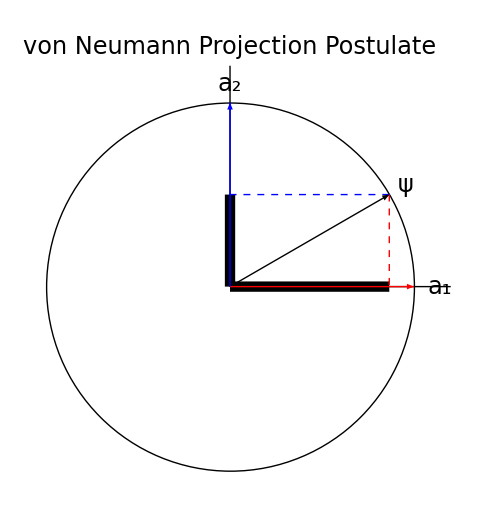

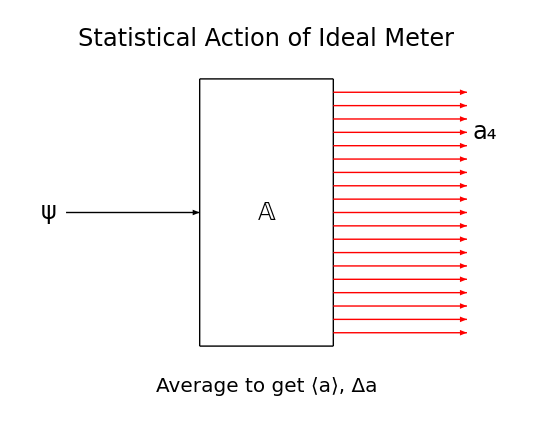

In the final pages of Mathematical Foundations … von Neumann sketches a dynamical model of the hypothetically abrupt & irreversible projective measurement process.

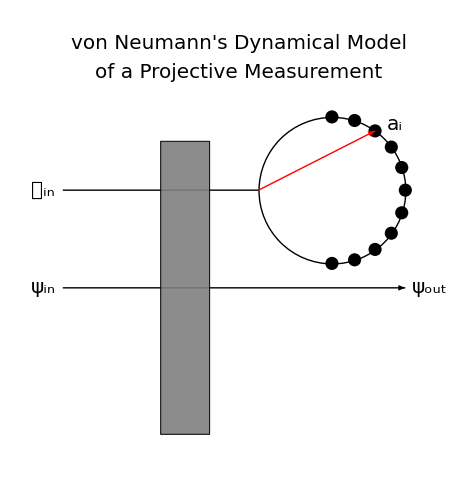

ψ [q]   :   Initial state of system 𝒮
ϕ [x]   :   Initial state of detector 𝒟, assumed to be a narrow Gaussian centered at x = 0
Ψ[q, x, 0] = ψ[q] ϕ[x]   :   Initial state of 𝒮⊗𝒟

Unitary evolution by 𝕌 (t) = Exp[-i ℍ t] with ℍ=-1/τℚ⊗ ℙ, where ℙ is momentum operator of "pointer."

Solve Schrödinger equation, get Ψ[q, x, t] = ψ[t] ϕ[x - q t/τ] which at time t = τ (end of measurement) becomes

Ψ[q,x,τ]=ψ[q]ϕ[x-q ]

Read "classical" meter projectively, get x=a_i. Means

ψ_out(q)≈ψ[q]× narrow Gaussian[q-a_1]

Unavoidable imprecision of detector means prepared state is actually a compact mixture. [I discussed "Quantum measurement with imprefect devices" at a Reed Physics seminar on 16 February 2000.] Here is a representation of what such a meter actually accomplishes:

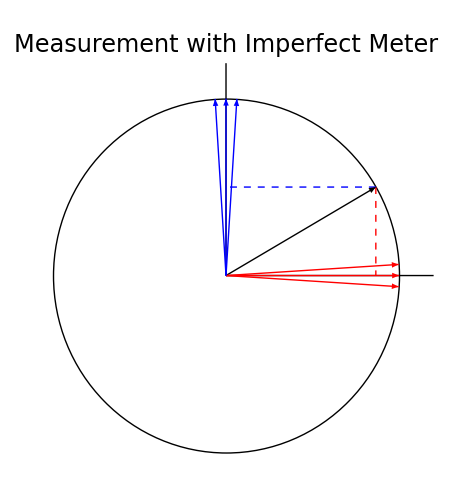

The results of A-measurements will be ambiguous if the spectrum of 𝔸 is degenerate. The projection postulate carries the implication that such ambiguity can be refined/resolved by subsequent  B-measurements if but only if 𝔸 and 𝔹 commute:

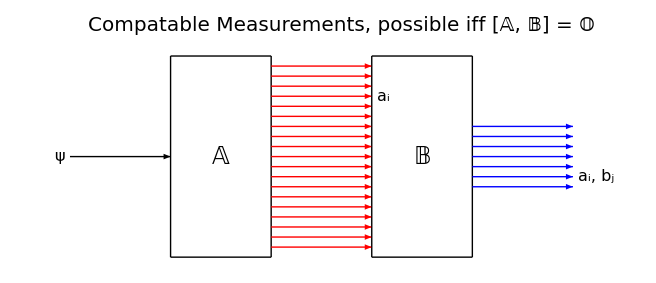

In 1927 the 26-year-old Werner Heisenberg (1902-1976)

saw that certain emergent difficulties in the quantum theory then under development by Bohr & Co. could be resolved if one accepted a principle of measurement-disturbance, which he formulated

Δ x Δ p ≈ ℏ

and later illustrated by analysis of the precision achievable with a "Heisenberg microscope":

REMARK: Heisenberg's rather vague analysis has been subjected to heavy criticism over the years, and in 2012 experimental results were reported that
surpassed the limit claimed by Heisenberg: see L. A. Rozema et al, "Violation  of Heisenberg's measurement-disturbance relationship by weak measurements," Phys. Rev. Letters 109, 100404 -1.

In 1925, Born & Jordan (and independently Dirac) came to the realization that the foundation of the "matrix mechanics" pioneered by Heisenberg earlier that same year resided in the commutation relation

[𝕏,ℙ]=iℏ𝕀

Several theorists undertook in 1928 to establish a link between that commutation relation and Heisenberg's Δ x Δ p ≈ ℏ. The definitive result was achieved by Schrödinger in 1932, who perfected ideas introduced by
E. U. Condon and by H. P. Robertson in 1929, and that had been brought to his attention by Arnold Sommerfeld.

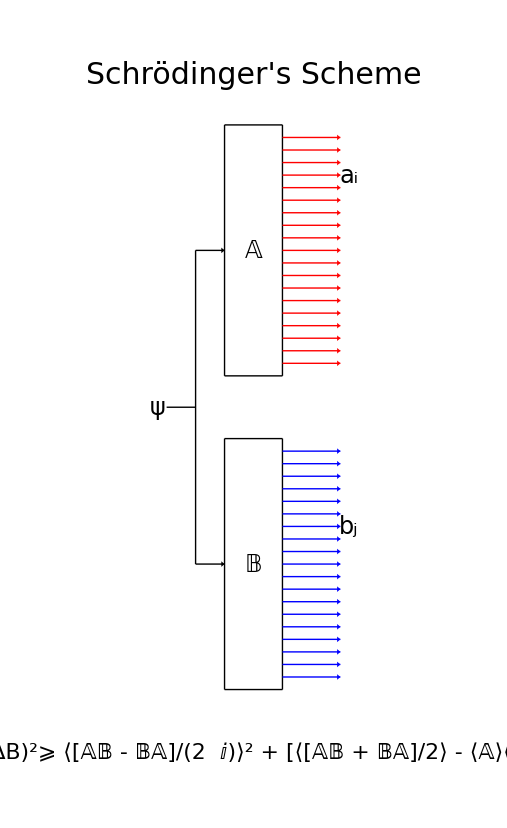

and can in the most familiar terms be phrased

((ΔXΔP))^2 ⩾ (ℏ/2)^2 + [⟨[𝕏ℙ+ℙ𝕏]/2⟩ - ⟨𝕏⟩⟨ℙ⟩]^2 ⩾ (ℏ/2)^2

Schrödinger and his predecessors built on a fact that emerges when the fundamental commutator is conjoined to implications of the projection postulate:

Conjugate observables cannot possess simultaneous eigenstates.

"Simultaneous" is used here in a sense distinct from that understood by Heisenberg when he spoke of a "measurement-disturbance relationship."  Schrödinger spoke (much more precisely than Heisenberg) of a relationship necessarily latent in

A-data collected on Monday, B-data collected on Tuesday

and went on to describe the minimal uncertainty states ("coherent states") that cause the quantum correlation term to vanish.

In 1965, two obscure engineers—E. Arthurs & J. L Kelly—at Bell Labs published in a relatively obscure journal (the Bell Labs Technichal Journal) a difficult-to-read article with the perplexing title "On the simultaneous measurement of a pair of conjugate observables." Their motivation was "determining the limitations of coherent quantum mechanical amplifiers, etc." 

Their essential idea (unstated): What one cannot do with perfect detectors one can attempt to do in a best-possible way with imperfect detectors.

Arthurs & Kelly proceeded in direct imitation of von  Neumann's dynamical argument:

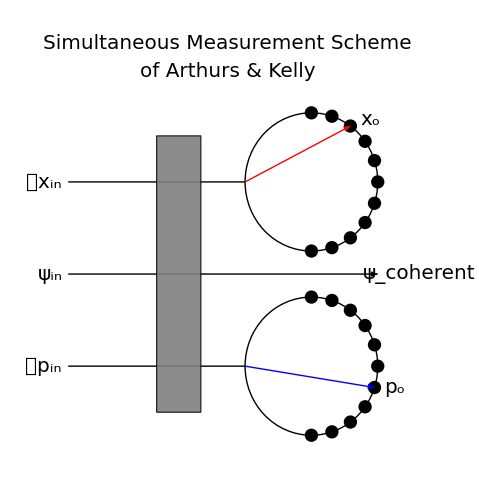

ψ[q]           :   Initial state of system 𝒮
ϕ_1[x]          :   Initial state of detector 𝒟_1
ϕ_2[y]          :   Initial state of detector 𝒟_2
Ψ[q, x, y, 0]   :   Initial state of composite system 𝒮⊗ 𝒟_1⊗ 𝒟_2

ℍ=1/τ{-λ_1ℚ⊗ℙ_1⊗𝕀-λ_2 ℙ⊗𝕀⊗ℙ_2}   :   Interaction Hamiltonian
ℚ and ℙ refer to 𝒮,  ℙ_1 refers to 𝒟_1,  ℙ_2 refers to 𝒟_2

Solve Schrödinger equation (and "elementry" but tricky business)

{∂_t +1/τ λ_1 q∂_x -i 1/τ λ_2∂_q ∂_y}Ψ[q,x,y,y]=0

subject to assumption that initial states of detectors are "balanced Gaussians"

ϕ_1[x]=(2/(π b))^(1/4)Exp[-x^2/b]     and      ϕ_2[y]=((2b)/π)^(1/4)Exp[-b y^2]

Read detectors at time t= τ, find pointers at positions x_m and y_m, giving

Ψ_out[q,x_m ,y_m]=(1/(π b))^(1/4)Exp[-(q-x_m)^2/(2b)+i q y_m]

These are eigenstates neither of position nor of momentum  but are Schrödinger's minimal uncertainty "coherent" states, that kill the quantum correlation. 

In the "phase space formulation of quantum mechanics" they acquire—via Wigner's construction (1932)

P_ψ[q,p]=(π ℏ)^-1∫OverBar[ψ[q+ξ]]e^(2(i/ℏ)p ξ)ψ[q-ξ]ⅆq

—the representation

P[q,p]=Exp[-(q-x_m)^2/b-b(p-y_m)^2]

where  (Δq)^2=1/2 b, (Δp)^2=1/2 b^-1 ⟹   Δq Δp=1/2.

Wigner quasi-distribution with x_m=2, y_m=1, b=0.5

Within a few months of the appearance of the Arthurs-Kelly paper two applied physicists at Stanford demonstrated (C. Y. She & H. Heffner, PR  152, 1103 (1966)) that their results could be obtained from a maximal entropy principle. But otherwise, the Arthurs-Kelly paper—now recognized to be a classic—was almost totally neglected.  Their results have now been reproduced by a great many alternative lines of argument.

## Slide 8

# Conclusion

At some early point in my career I dismissed—perhaps too facilely—literature relating to foundational matters in physics as "so much inconclusive philosophical verbiage that could be safely ignored," a waste of time to pursue.  That is no longer so. It was arguably John S. Bell who changed all of that, who rendered the foundational studies subject to explicit calculation and experiment. 

Insights have in recent decades been developed and are today being cultivated that lie beyond the reach of contemporary textbooks but that—after they have been distilled—will, I am convinced, be prominent in the quantum texts (and philosophical monographs) of the future. I speak of developments that have been inspired by recognition of the role that information-theoretic notions are destined to play, by the expanding importance of entanglement physics, by the technical requirements of quantum computation. 

My effort here has been to demonstrate that some of those developments (many of which have deep historical roots, however exotically strange they may at first sight appear) are already quite accessible, even to undergraduates.

# Things to Read

Heinz-Peter  Breuer & Francesco Petruccione, The Theory of Open Quantum Systems (Oxford, 2006).

Stephen M. Barnett, Quantum Information (Oxford, 2009).

Maximilian Schlosshauer, Decoherence and the Quantum-to-Classical Transition (Springer, 2008).

Domenico  Guilini, Erich Joos, Claus  Kiefer, Joachim Kupsch, Ion-Olimpiu Stamatescu & Heinzx-Dieter Zeh, Decoherence and the Appearance of a Classical World in Quantum Theory, Springer (1996).

Christopher Gerry & Peter Knight, Introductory Quantum Optics (Cambridge, 2005).

Michael A. Nielsen & Isaac L. Chuang, Quantum Computation and Quantum Information (Cambridge, 2000).

Wojciech H. Zurek (editor), Complexity, Entropy and the Physics of Information; Volume VIII, Santa Fe Institute Studies in the Sciences of Complexity (Addison-Wesley, 1990), proceedings of a workshop held 
29 May-10 June 1989 to which many of the leading figures in the field made contributions.

Wojciech H. Zurek, "Decoherence and the transition from quantum to classical—Revisited," Los Alamos Science, Number 27 (2002, available on the web).

E. Arthurs & J. L. Kelly Jr, "On the simultaneous measurement of a pair of conjugate observables," Bell System Tech. J. 44, 725 (1965).

N. A. Wheeler, "Simultaneous measurement of noncommuting quantum observables" (October, 2012); pdf file available by request.

N. A. Wheeler, "Harmonic oscillator—revisited: coherent states," 
(December, 2012); pdf file available by request.

Those books and papers provide references to a vast and rapidly growing literature. Consult the web for lists of the publications by (for example) 
   • Wojciech Zurek
   • William Wooters
   • Asher Peres
   • Reinhard Werner
   • Anton Zeilinger